```mathematica
(*Mathematica*)
```

```mathematica
Clear[ϕ,f]
```

```mathematica
ϕ=N[GoldenRatio]
```

1.61803

```mathematica
Exp[2*π*I*ϕ]
```

-0.737369-0.67549 ⅈ

```mathematica
CompanionMatrix[p_, x_] := Module[{cl=CoefficientList[p, x], deg, m}, cl=Drop[cl/Last[cl], -1]; deg=Length[cl]; If[deg==1, {-cl}, m=RotateLeft[IdentityMatrix[deg]]; m[[ -1]]=-cl; Transpose[m]]];
```

```mathematica
m=Transpose[CompanionMatrix[(x+1)(x^3-1),x]]
```

{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,1,0,-1}}

```mathematica
N[Eigenvalues[m]]
```

{-1.,1.,-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ}

```mathematica
Apply[Plus,N[Eigenvalues[m]]]
```

-1.+2.22045×10^-16 ⅈ

```mathematica
r[i_]:=x/.NSolve[(x+1)(x^3-1)==0,x][[i]]
```

```mathematica
v=Table[r[i],{i,4}]
```

{-1.,-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ,1.}

```mathematica
Abs[%]
```

{1.,1.,1.,1.}

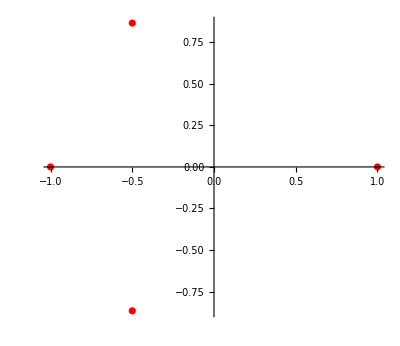

```mathematica
ComplexListPlot[v,PlotStyle->Red]
```

```mathematica
sc=2.0;
```

```mathematica
w={{{Re[r[1]],Im[r[1]]},{Re[r[2]],Im[r[2]]}},{{Re[r[1]],Im[r[1]]},{Re[r[3]],Im[r[3]]}},{{Re[r[1]],Im[r[1]]},{Re[r[2]],Im[r[2]]}},{{Re[r[2]],Im[r[2]]},{Re[r[3]],Im[r[3]]}},{{Re[r[2]],Im[r[2]]},{Re[r[4]],Im[r[4]]}},{{Re[r[3]],Im[r[3]]},{Re[r[4]],Im[r[4]]}}}
```

{{{-1.,0},{-0.5,-0.866025}},{{-1.,0},{-0.5,0.866025}},{{-1.,0},{-0.5,-0.866025}},{{-0.5,-0.866025},{-0.5,0.866025}},{{-0.5,-0.866025},{1.,0}},{{-0.5,0.866025},{1.,0}}}

```mathematica
Table[Eigenvalues[w[[i]]],{i,6}]
```

{{-1.,-0.866025},{-1.,0.866025},{-1.,-0.866025},{1.13144,-0.765417},{-0.25+0.896396 ⅈ,-0.25-0.896396 ⅈ},{-1.2136,0.7136}}

```mathematica
(* Projecting the Limiting Cyclic3 Polynomial onto a quartic Hermann rings Julia*)
```

```mathematica
f[z_,1]=Exp[2*π*I*ϕ]*z^4*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)/((-(sc*r[1]*z)^2+1)(-(sc*r[2]*z)^2+1));
f[z_,2]=Exp[2*π*I*ϕ]*z^4*(z^2-(sc*r[1])^2)*(z^2-(sc*r[3])^2)/((-(sc*r[1]*z)^2+1)(-(sc*r[3]*z)^2+1));
f[z_,3]=Exp[2*π*I*ϕ]*z^4*(z^2-(sc*r[1])^2)*(z^2-(sc*r[4])^2)/((-(sc*r[1]*z)^2+1)(-(sc*r[4]*z)^2+1));
f[z_,4]=Exp[2*π*I*ϕ]*z^4*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)/((-(sc*r[2]*z)^2+1)(-(sc*r[3]*z)^2+1));
f[z_,5]=Exp[2*π*I*ϕ]*z^4*(z^2-(sc*r[2])^2)*(z^2-(sc*r[4])^2)/((-(sc*r[2]*z)^2+1)(-(sc*r[4]*z)^2+1));
f[z_,6]=Exp[2*π*I*ϕ]*z^4*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)/((-(sc*r[3]*z)^2+1)(-(sc*r[4]*z)^2+1));
```

```mathematica
g=Table[JuliaSetPlot[f[z,i],z, Method -> "OrbitDetection",ColorFunction->Hue,ImageSize->2000,PlotStyle->{Opacity[0.2],Red,PointSize[0.0005]},AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality","Bound"->12,Frame->False,PlotRange->All],{i,6}];
```

```mathematica
Export["Julia_Quartic_cyclic3Polynomial_Herman_rings_Hue_scale2.jpg",GraphicsGrid[{{g[[1]],g[[2]],g[[3]]},{g[[4]],g[[5]],g[[6]]}},ImageSize->{6000,4000}]]
```

Julia_Quartic_cyclic3Polynomial_Herman_rings_Hue_scale2.jpg

```mathematica
(*end*)
```